```mathematica
Clear["Global`*"]
```

```mathematica
sinusoid[t_]:=r*Sqrt[a^2+b^2]*Sin[w*t+ArcTan[a,b]]
```

```mathematica
line[t_]:=a*x0+b*y0+c*z0-c*t
```

```mathematica
diff[t_]:=sinusoid[t]-line[t]
```

```mathematica
a:=1
b:=1
c:=1
x0:=1
y0:=1
z0:=1
r:=3
w:=1
```

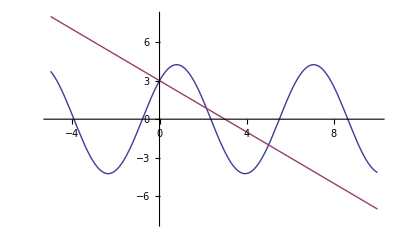

```mathematica
Plot[{sinusoid[t],line[t]},{t,-5,10},PlotRange->{-8,8}]
```

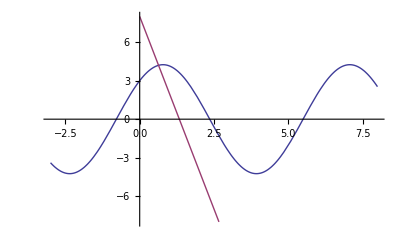

```mathematica
Plot[{sinusoid[t],line[t]},{t,-5,10},PlotRange->{-8,8},GridLines-> {{-1.245},{r*Sqrt[a^2+b^2],-r*Sqrt[a^2+b^2]}}]
```

-Graphics-

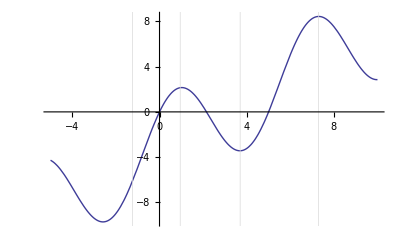

```mathematica
Plot[diff[t],{t,-5,10},GridLines->{{-1.245,.95,3.7,7.3},{}}]
```

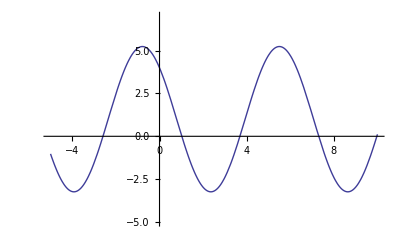

```mathematica
Plot[diff'[t],{t,-5,10},PlotRange->{-5,7}]
```

```mathematica
helix=ParametricPlot3D[{r*Cos[w*t],r*Sin[w*t],t},{t,-5,10}]
```

-Graphics3D-

```mathematica
plane=ContourPlot3D[a*(x-x0)+b*(y-y0)+a*(z-z0)==0,{x,-10,10},{y,-10,10},{z,-20,20}]
```

-Graphics3D-

```mathematica
points=Graphics3D[{PointSize[Large],Red, Point[{3,0,0}], Red, Point[{-1.6569,2.50096,2.155902}], Point[{0.86664,-2.8721,5.0054}]}]
```

-Graphics3D-

```mathematica
Show[helix,plane,points,PlotRange->{{-5,5},{-5,5},{-5,10}}]
```

-Graphics3D-

```mathematica
N[1/w*(ArcSin[(a*x0+b*y0)/(r*Sqrt[a^2+b^2])]-ArcTan[a,b])]
```

-0.294515